```mathematica
μextreme[uh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]/uh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
qcrit[us_,uh_,μ_,z_,θ_]:=us^(θ/2-z)Sqrt[1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z))]/(μ(1-(us/uh)^(z-θ)));
uz1[q_,us_,uh_,μ_,z_,θ_]:=NDSolveValue[
{-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) (((-2-z+θ) u[t]^(3-2 z) (u[t]/uh)^(z-θ))/uh^2-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(3-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(3-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)+(2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+((-((2+z-θ) (u[t]/uh)^(1+z-θ))/uh-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(1+2 z-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(1+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)) u'[t]^2)/(-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^(3-2 z) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0,u[0]== us,u'[0]==0},u,{t,0.1,5.7}
];
fu1[t_,q_,us_,uh_,μ_,z_,θ_]:=uz1[q,us,uh,μ,z,θ][t];
dfu1[t_,q_,us_,uh_,μ_,z_,θ_]:=D[uz1[q,us,uh,μ,z,θ][t1],t1]/.{t1->t};
pu[t_,q_,us_,uh_,μ_,z_,θ_]:=Block[
{du,u,fu},
du=dfu1[t,q,us,uh,μ,z,θ];
u=fu1[t,q,us,uh,μ,z,θ];
fu=1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z));
Return[u^(θ/2-1)du/(fu Sqrt[u^(2(1-z))fu - du^2/fu])];
];
```

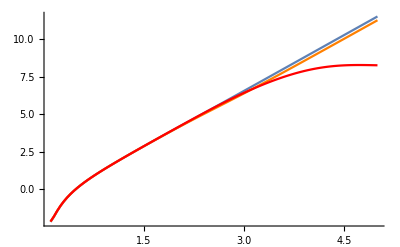

```mathematica
Show[
ListLinePlot[Table[{i,-(Abs[pu[i,20,0.1,1,0.75μextreme[1,1.5,0.1800],1.5,0.1800]]//Log)},{i,0.1,5,0.05}]],
ListLinePlot[Table[{i,-(Abs[pu[i,20,0.1,1,0.75μextreme[1,1.5,0.1950],1.5,0.1950]]//Log)},{i,0.1,5,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,-(Abs[pu[i,20,0.1,1,0.75μextreme[1,1.5,0.1991],1.5,0.1991]]//Log)},{i,0.1,5,0.05}],PlotStyle->Red],
PlotRange->{{0.1,5},All},AxesOrigin->{0,0}
]
```

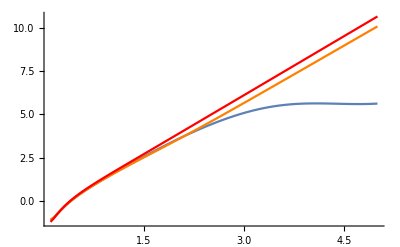

```mathematica
Show[
ListLinePlot[Table[{i,-(Abs[pu[i,10,0.1,1,0.75μextreme[1,1.5389,1.0],1.5389,1.0]]//Log)},{i,0.1,5,0.05}]],
ListLinePlot[Table[{i,-(Abs[pu[i,10,0.1,1,0.75μextreme[1,1.55,1.0],1.55,1.0]]//Log)},{i,0.1,5,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,-(Abs[pu[i,10,0.1,1,0.75μextreme[1,1.60,1.0],1.60,1.0]]//Log)},{i,0.1,5,0.05}],PlotStyle->Red],
PlotRange->{{0.1,5},All},AxesOrigin->{0,0}
]
```

```mathematica
Table[{i,Abs[(Abs[pu[i,20,0.1,1,0.75μextreme[1,1.5,0.1800],1.5,0.1800]]//Log)]},{i,0.1,5,0.05}]
```

{{0.1,2.19392},{0.15,1.85472},{0.2,1.46999},{0.25,1.12601},{0.3,0.827911},{0.35,0.56699},{0.4,0.334653},{0.45,0.124228},{0.5,0.0692533},{0.55,0.249497},{0.6,0.419295},{0.65,0.580781},{0.7,0.735601},{0.75,0.885041},{0.8,1.03011},{0.85,1.17161},{0.9,1.31019},{0.95,1.44634},{1.,1.58048},{1.05,1.71293},{1.1,1.84396},{1.15,1.97379},{1.2,2.10258},{1.25,2.23048},{1.3,2.3576},{1.35,2.48404},{1.4,2.60986},{1.45,2.73514},{1.5,2.85993},{1.55,2.9843},{1.6,3.10827},{1.65,3.2319},{1.7,3.35523},{1.75,3.47829},{1.8,3.60115},{1.85,3.72382},{1.9,3.84636},{1.95,3.96879},{2.,4.09116},{2.05,4.2135},{2.1,4.33584},{2.15,4.45819},{2.2,4.58059},{2.25,4.70306},{2.3,4.82559},{2.35,4.94823},{2.4,5.07095},{2.45,5.19377},{2.5,5.3167},{2.55,5.43971},{2.6,5.56283},{2.65,5.68605},{2.7,5.80936},{2.75,5.93275},{2.8,6.05622},{2.85,6.17978},{2.9,6.3034},{2.95,6.42708},{3.,6.55083},{3.05,6.67463},{3.1,6.79848},{3.15,6.92237},{3.2,7.0463},{3.25,7.17027},{3.3,7.29427},{3.35,7.4183},{3.4,7.54236},{3.45,7.66643},{3.5,7.79053},{3.55,7.91464},{3.6,8.03872},{3.65,8.16294},{3.7,8.28706},{3.75,8.41124},{3.8,8.53547},{3.85,8.65961},{3.9,8.78387},{3.95,8.90807},{4.,9.03234},{4.05,9.15691},{4.1,9.28067},{4.15,9.40482},{4.2,9.52913},{4.25,9.6533},{4.3,9.77759},{4.35,9.90195},{4.4,10.0262},{4.45,10.1503},{4.5,10.2746},{4.55,10.3989},{4.6,10.5233},{4.65,10.6474},{4.7,10.7716},{4.75,10.8959},{4.8,11.0201},{4.85,11.1442},{4.9,11.2684},{4.95,11.3929},{5.,11.5172}}

```mathematica
Table[{i,-(Abs[pu[i,20,0.1,1,0.75μextreme[1,1.5,0.1800],1.5,0.1800]]//Log)},{i,0.1,5,0.05}]
```

{{0.1,-2.19392},{0.15,-1.85472},{0.2,-1.46999},{0.25,-1.12601},{0.3,-0.827911},{0.35,-0.56699},{0.4,-0.334653},{0.45,-0.124228},{0.5,0.0692533},{0.55,0.249497},{0.6,0.419295},{0.65,0.580781},{0.7,0.735601},{0.75,0.885041},{0.8,1.03011},{0.85,1.17161},{0.9,1.31019},{0.95,1.44634},{1.,1.58048},{1.05,1.71293},{1.1,1.84396},{1.15,1.97379},{1.2,2.10258},{1.25,2.23048},{1.3,2.3576},{1.35,2.48404},{1.4,2.60986},{1.45,2.73514},{1.5,2.85993},{1.55,2.9843},{1.6,3.10827},{1.65,3.2319},{1.7,3.35523},{1.75,3.47829},{1.8,3.60115},{1.85,3.72382},{1.9,3.84636},{1.95,3.96879},{2.,4.09116},{2.05,4.2135},{2.1,4.33584},{2.15,4.45819},{2.2,4.58059},{2.25,4.70306},{2.3,4.82559},{2.35,4.94823},{2.4,5.07095},{2.45,5.19377},{2.5,5.3167},{2.55,5.43971},{2.6,5.56283},{2.65,5.68605},{2.7,5.80936},{2.75,5.93275},{2.8,6.05622},{2.85,6.17978},{2.9,6.3034},{2.95,6.42708},{3.,6.55083},{3.05,6.67463},{3.1,6.79848},{3.15,6.92237},{3.2,7.0463},{3.25,7.17027},{3.3,7.29427},{3.35,7.4183},{3.4,7.54236},{3.45,7.66643},{3.5,7.79053},{3.55,7.91464},{3.6,8.03872},{3.65,8.16294},{3.7,8.28706},{3.75,8.41124},{3.8,8.53547},{3.85,8.65961},{3.9,8.78387},{3.95,8.90807},{4.,9.03234},{4.05,9.15691},{4.1,9.28067},{4.15,9.40482},{4.2,9.52913},{4.25,9.6533},{4.3,9.77759},{4.35,9.90195},{4.4,10.0262},{4.45,10.1503},{4.5,10.2746},{4.55,10.3989},{4.6,10.5233},{4.65,10.6474},{4.7,10.7716},{4.75,10.8959},{4.8,11.0201},{4.85,11.1442},{4.9,11.2684},{4.95,11.3929},{5.,11.5172}}

```mathematica
Table[{i,pu[i,20,0.1,1,0.75μextreme[1,1.5,0.1800],1.5,0.1800]},{i,0.1,5,0.05}]
```

{{0.1,8.9703+0. ⅈ},{0.15,6.38988+0. ⅈ},{0.2,4.34921+0. ⅈ},{0.25,3.08334+0. ⅈ},{0.3,2.28853+0. ⅈ},{0.35,1.76295+0. ⅈ},{0.4,1.39746+0. ⅈ},{0.45,1.13227+0. ⅈ},{0.5,0.93309+0. ⅈ},{0.55,0.779193+0. ⅈ},{0.6,0.65751+0. ⅈ},{0.65,0.559461+0. ⅈ},{0.7,0.479217+0. ⅈ},{0.75,0.412697+0. ⅈ},{0.8,0.356967+0. ⅈ},{0.85,0.309866+0. ⅈ},{0.9,0.26977+0. ⅈ},{0.95,0.235431+0. ⅈ},{1.,0.205877+0. ⅈ},{1.05,0.180337+0. ⅈ},{1.1,0.158189+0. ⅈ},{1.15,0.138929+0. ⅈ},{1.2,0.12214+0. ⅈ},{1.25,0.107476+0. ⅈ},{1.3,0.0946468+0. ⅈ},{1.35,0.083406+0. ⅈ},{1.4,0.0735449+0. ⅈ},{1.45,0.0648849+0. ⅈ},{1.5,0.0572725+0. ⅈ},{1.55,0.0505751+0. ⅈ},{1.6,0.0446783+0. ⅈ},{1.65,0.0394825+0. ⅈ},{1.7,0.0349015+0. ⅈ},{1.75,0.03086+0. ⅈ},{1.8,0.0272924+0. ⅈ},{1.85,0.0241416+0. ⅈ},{1.9,0.0213574+0. ⅈ},{1.95,0.0188962+0. ⅈ},{2.,0.0167198+0. ⅈ},{2.05,0.0147945+0. ⅈ},{2.1,0.0130909+0. ⅈ},{2.15,0.0115833+0. ⅈ},{2.2,0.0102488+0. ⅈ},{2.25,0.00906751+0. ⅈ},{2.3,0.00802179+0. ⅈ},{2.35,0.00709599+0. ⅈ},{2.4,0.00627642+0. ⅈ},{2.45,0.00555105+0. ⅈ},{2.5,0.00490894+0. ⅈ},{2.55,0.00434074+0. ⅈ},{2.6,0.0038379+0. ⅈ},{2.65,0.00339298+0. ⅈ},{2.7,0.00299936+0. ⅈ},{2.75,0.00265118+0. ⅈ},{2.8,0.00234323+0. ⅈ},{2.85,0.00207089+0. ⅈ},{2.9,0.00183007+0. ⅈ},{2.95,0.00161716+0. ⅈ},{3.,0.00142893+0. ⅈ},{3.05,0.00126254+0. ⅈ},{3.1,0.00111547+0. ⅈ},{3.15,0.00098549+0. ⅈ},{3.2,0.000870622+0. ⅈ},{3.25,0.000769114+0. ⅈ},{3.3,0.00067942+0. ⅈ},{3.35,0.000600168+0. ⅈ},{3.4,0.000530147+0. ⅈ},{3.45,0.000468285+0. ⅈ},{3.5,0.000413634+0. ⅈ},{3.55,0.000365354+0. ⅈ},{3.6,0.000322722+0. ⅈ},{3.65,0.000285024+0. ⅈ},{3.7,0.000251754+0. ⅈ},{3.75,0.000222355+0. ⅈ},{3.8,0.000196378+0. ⅈ},{3.85,0.000173452+0. ⅈ},{3.9,0.000153185+0. ⅈ},{3.95,0.000135293+0. ⅈ},{4.,0.000119483+0. ⅈ},{4.05,0.000105489+0. ⅈ},{4.1,0.0000932084+0. ⅈ},{4.15,0.0000823263+0. ⅈ},{4.2,0.0000727026+0. ⅈ},{4.25,0.0000642135+0. ⅈ},{4.3,0.000056708+0. ⅈ},{4.35,0.0000500771+0. ⅈ},{4.4,0.000044227+0. ⅈ},{4.45,0.0000390633+0. ⅈ},{4.5,0.0000345+0. ⅈ},{4.55,0.0000304669+0. ⅈ},{4.6,0.0000269033+0. ⅈ},{4.65,0.0000237625+0. ⅈ},{4.7,0.0000209872+0. ⅈ},{4.75,0.0000185341+0. ⅈ},{4.8,0.0000163695+0. ⅈ},{4.85,0.0000144583+2.13748×10^-14 ⅈ},{4.9,0.00001277+3.35694×10^-14 ⅈ},{4.95,0.0000112756-1.45795×10^-14 ⅈ},{5.,9.95762×10^-6+7.5922×10^-14 ⅈ}}

```mathematica
βpu[t_,q_,us_,uh_,μ_,z_,θ_]:=Block[
{du,u,fu,β},
du=dfu1[t,q,us,uh,μ,z,θ];
u=fu1[t,q,us,uh,μ,z,θ];
fu=1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z));
β=1/(D[1-(u1/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) u1^(2(z-θ+1))/uh^(2z-2θ)(1-(u1/uh)^(θ-z)),u1]/.{u1-> us});
Return[β u^(θ/2-1)du/(fu Sqrt[u^(2(1-z))fu - du^2/fu])];
];
```

```mathematica
Table[{i,βpu[i,20,0.1,1,0.75μextreme[1,1.5,0.1800],1.5,0.1800]},{i,0.1,5,0.05}]
```

{{0.1,-355.014+0. ⅈ},{0.15,-252.89+0. ⅈ},{0.2,-172.127+0. ⅈ},{0.25,-122.028+0. ⅈ},{0.3,-90.5723+0. ⅈ},{0.35,-69.7717+0. ⅈ},{0.4,-55.3065+0. ⅈ},{0.45,-44.8116+0. ⅈ},{0.5,-36.9285+0. ⅈ},{0.55,-30.8378+0. ⅈ},{0.6,-26.022+0. ⅈ},{0.65,-22.1416+0. ⅈ},{0.7,-18.9658+0. ⅈ},{0.75,-16.3332+0. ⅈ},{0.8,-14.1275+0. ⅈ},{0.85,-12.2634+0. ⅈ},{0.9,-10.6766+0. ⅈ},{0.95,-9.31755+0. ⅈ},{1.,-8.14791+0. ⅈ},{1.05,-7.13711+0. ⅈ},{1.1,-6.26059+0. ⅈ},{1.15,-5.49834+0. ⅈ},{1.2,-4.8339+0. ⅈ},{1.25,-4.25355+0. ⅈ},{1.3,-3.7458+0. ⅈ},{1.35,-3.30092+0. ⅈ},{1.4,-2.91066+0. ⅈ},{1.45,-2.56792+0. ⅈ},{1.5,-2.26665+0. ⅈ},{1.55,-2.00159+0. ⅈ},{1.6,-1.76821+0. ⅈ},{1.65,-1.56258+0. ⅈ},{1.7,-1.38128+0. ⅈ},{1.75,-1.22133+0. ⅈ},{1.8,-1.08014+0. ⅈ},{1.85,-0.955441+0. ⅈ},{1.9,-0.845254+0. ⅈ},{1.95,-0.747849+0. ⅈ},{2.,-0.661712+0. ⅈ},{2.05,-0.585515+0. ⅈ},{2.1,-0.518095+0. ⅈ},{2.15,-0.458427+0. ⅈ},{2.2,-0.405613+0. ⅈ},{2.25,-0.358861+0. ⅈ},{2.3,-0.317475+0. ⅈ},{2.35,-0.280835+0. ⅈ},{2.4,-0.2484+0. ⅈ},{2.45,-0.219692+0. ⅈ},{2.5,-0.194279+0. ⅈ},{2.55,-0.171792+0. ⅈ},{2.6,-0.151891+0. ⅈ},{2.65,-0.134283+0. ⅈ},{2.7,-0.118704+0. ⅈ},{2.75,-0.104925+0. ⅈ},{2.8,-0.0927372+0. ⅈ},{2.85,-0.0819587+0. ⅈ},{2.9,-0.072428+0. ⅈ},{2.95,-0.0640016+0. ⅈ},{3.,-0.0565523+0. ⅈ},{3.05,-0.0499671+0. ⅈ},{3.1,-0.0441465+0. ⅈ},{3.15,-0.0390023+0. ⅈ},{3.2,-0.0344563+0. ⅈ},{3.25,-0.0304389+0. ⅈ},{3.3,-0.0268891+0. ⅈ},{3.35,-0.0237526+0. ⅈ},{3.4,-0.0209814+0. ⅈ},{3.45,-0.0185331+0. ⅈ},{3.5,-0.0163702+0. ⅈ},{3.55,-0.0144595+0. ⅈ},{3.6,-0.0127722+0. ⅈ},{3.65,-0.0112803+0. ⅈ},{3.7,-0.00996355+0. ⅈ},{3.75,-0.00880004+0. ⅈ},{3.8,-0.00777196+0. ⅈ},{3.85,-0.00686463+0. ⅈ},{3.9,-0.00606253+0. ⅈ},{3.95,-0.00535444+0. ⅈ},{4.,-0.00472873+0. ⅈ},{4.05,-0.00417488+0. ⅈ},{4.1,-0.00368887+0. ⅈ},{4.15,-0.0032582+0. ⅈ},{4.2,-0.00287732+0. ⅈ},{4.25,-0.00254135+0. ⅈ},{4.3,-0.00224431+0. ⅈ},{4.35,-0.00198188+0. ⅈ},{4.4,-0.00175035+0. ⅈ},{4.45,-0.00154599+0. ⅈ},{4.5,-0.00136539+0. ⅈ},{4.55,-0.00120578+0. ⅈ},{4.6,-0.00106474+0. ⅈ},{4.65,-0.00094044+0. ⅈ},{4.7,-0.000830602+0. ⅈ},{4.75,-0.000733515+0. ⅈ},{4.8,-0.00064785+0. ⅈ},{4.85,-0.000572209-8.45942×10^-13 ⅈ},{4.9,-0.000505395-1.32856×10^-12 ⅈ},{4.95,-0.000446249+5.77008×10^-13 ⅈ},{5.,-0.000394089-3.00473×10^-12 ⅈ}}

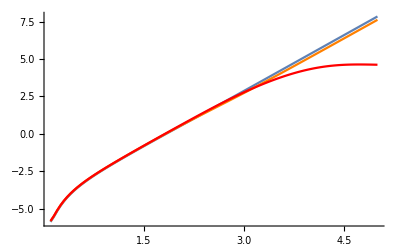

```mathematica
Show[
ListLinePlot[Table[{i,-(Abs[βpu[i,20,0.1,1,0.75μextreme[1,1.5,0.1800],1.5,0.1800]]//Log)},{i,0.1,5,0.05}]],
ListLinePlot[Table[{i,-(Abs[βpu[i,20,0.1,1,0.75μextreme[1,1.5,0.1950],1.5,0.1950]]//Log)},{i,0.1,5,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,-(Abs[βpu[i,20,0.1,1,0.75μextreme[1,1.5,0.1991],1.5,0.1991]]//Log)},{i,0.1,5,0.05}],PlotStyle->Red],
PlotRange->{{0.1,5},All},AxesOrigin->{0,0}
]
```

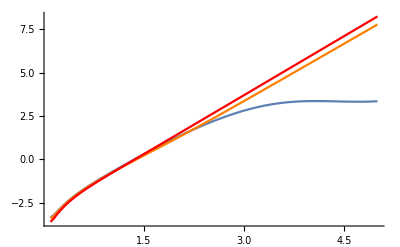

```mathematica
Show[
ListLinePlot[Table[{i,-(Abs[βpu[i,10,0.1,1,0.75μextreme[1,1.5389,1.0],1.5389,1.0]]//Log)},{i,0.1,5,0.05}]],
ListLinePlot[Table[{i,-(Abs[βpu[i,10,0.1,1,0.75μextreme[1,1.5500,1.0],1.5500,1.0]]//Log)},{i,0.1,5,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,-(Abs[βpu[i,10,0.1,1,0.75μextreme[1,1.6000,1.0],1.6000,1.0]]//Log)},{i,0.1,5,0.05}],PlotStyle->Red],
PlotRange->{{0.1,5},All},AxesOrigin->{0,0}
]
```

```mathematica
-(Abs[-0.01]//Log)
```

4.60517